```mathematica
L=1;
l = 0.3;
f=1;
e=1;
A=1;
ρ=1;
a=√(e A/ρ);
T=3;
```

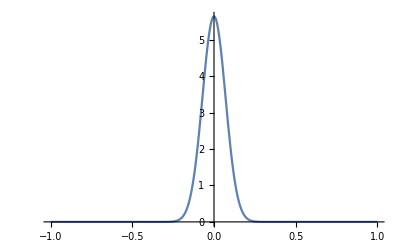

```mathematica
appro=With[{k=10},Erf[k #]/2+1/2&];
Plot[appro'[x - 0], {x, -1, 1}, PlotRange -> All]
```

### Use NDSolve to get the numerical result of PDE

```mathematica
s=NDSolve[{D[u[t,x], t,t]==a^2 D[u[t,x], x,x]+f/ρ DiracDelta[x-l],u[0,x]==0,Derivative[1,0][u][0,x]==0,u[t,0]==u[t,L]==0}/.{DiracDelta->appro'},u,{t,0,T},{x,0,L}];
```

NDSolve::eerr: 警告：在自变量 x 的方向上位于 t = 3. 处的 19.8381 的经过尺度缩放的局部误差估计比规定的误差容差大很多. 25 个点的网格间隔可能太大，因此无法达到预期的准确度或者精度. 可能已经形成了奇点，或者您可能需要使用 MaxStepSize 或者 MinPoints 方法选项指定一个更小的网格间隔.

-Graphics3D-

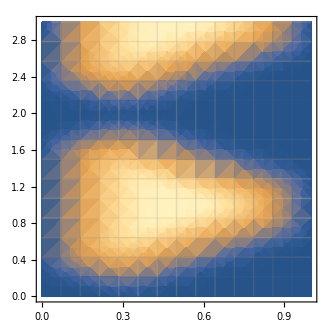

```mathematica
Plot3D[Evaluate[u[t,x]/.s],{t,0,T},{x,0,L},AxesLabel->Automatic, PlotTheme->"Classic"]
DensityPlot[Evaluate[u[t,x]/.s],{x,0,L},{t,0,T},Mesh->Full]
```

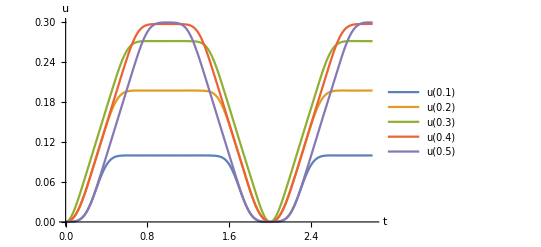

```mathematica
F[x1_,t1_]=((u[t,x])/.s)/.{x->x1,t->t1};
Plot[{F[0.1,t],F[0.2,t],F[0.3,t],F[0.4,t],F[0.5,t]},{t,0,3},PlotRange->All,AxesLabel->{"t","u"},PlotLegends->{"u(0.1)","u(0.2)","u(0.3)","u(0.4)","u(0.5)"}]
```